## Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/GradientDescend.wls"
```

/home/juanathan/gdrive/Collaborations/2022-06 INAOE/2-Reflectance_Measurments_NormalDist

```mathematica
fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
```

## Sample Characteristics

```mathematica
film = Import[#,"Data"]& @@ FileNames["1*fill.csv"];
TableForm[film[[2;;]],TableHeadings->{None,film[[1]]}]
radius = film[[2;;,2]];
muSigma = film[[2;;,{2,3}]];
cfrac = film[[2;;,4]]/100;
```

Nominal Au Thickness [+-0.2 nm] | Mean radius [nm] |  | Fill factor [100%] | 
3 | 5.78 | 1.89 | 20.3 | 0.6
5 | 7.3 | 2.3 | 22.1 | 0.1

```mathematica
nMat  = Import[#,"Data"] & @@ FileNames["3*Ind.csv"];
nMat = Drop[nMat,1];
nM = nMat[[1,2]]
```

1.33278

## Experimental Spectra AuNI

```mathematica
(files = FileNames["*","Extinction*"])//TableForm
data = Import[#,"Data"]& /@ files;
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
nNP=JohnsonChristyAuRefSize[#1,#2]&;
pl = MapThread[Style["a = "<>ToString[#1]<>" nm, Θ = "<> ToString[#2],texStyle]&,{radius,cfrac}];
labels = Outer[#1<>" - θ_i = "<>#2<>"°"&,{"s-pol","p-pol"},ToString/@(ang*180/Pi)];
```

Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 64_9deg.xlsx
Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 72_9deg.xlsx

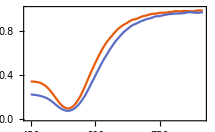
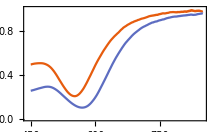
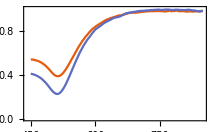
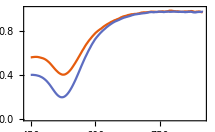

```mathematica
spectra = Map[Drop[#,4]&, data,{2}] (*Delete Headers*) ;
spectra = Map[Select[#,Function[list,wlL<=list[[1]]<= wlR]]&,spectra,{2}](*Choosing in the Visible*);
spectra = Map[Table[#[[{1,i}]]*{1,.01},{i,2,Length[#]}]&,spectra,{3}];
spectra = Transpose[spectra,{2,1,4,3,5}](*[[pol, ang, thickness, lda, Ext]]*);
spectra=spectra[[;;,;;,{1,2}]];

islandExt = Map[ListLinePlot[#,Evaluate[graphsOptsExp],PlotRange->{0,1}]&,spectra,{2}]
```

## Poly

```mathematica
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
```

```mathematica
nominal = MapThread[ (
mu = First[#1];
sigma = Last[#1];
indAu = Transpose[Table[{nM,1.5},{i,wlen}]];
			norm2[CSMBioReflectionInt[ang,indAu,wlen,#2,{mu,sigma},"SizeDistribution"->"Normal"]])&,
{muSigma,cfrac}]; (*[[case, pol,ang,lda]]*)

nominal = Transpose[nominal,{3,1,2,4}](*[[pol,ang, case,lda]]*);
nominalplots = MapThread[ListLinePlot[#1,PlotLabel->#2,  DataRange->wlen[[{1,-1}]],PlotStyle->Dotted,Evaluate[graphsOptsTeo]]&,{nominal,labels},2];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

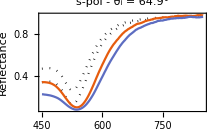
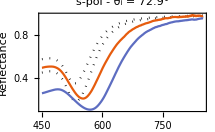
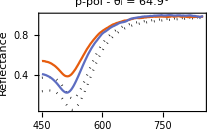
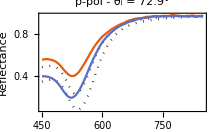

```mathematica
MapThread[Show[{#1,#2},PlotRange->All, FrameLabel-> (Style[#,texStyle]&/@{"Wavelength [nm]","Reflectance"})]&,{nominalplots,islandExt},2]
```

## FitModel (Gradient Descend) p Pol

{2,2,2,3138,2}

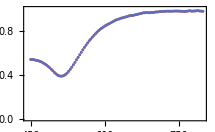
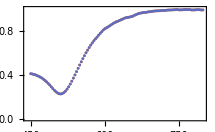
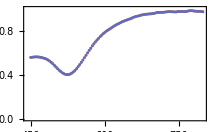
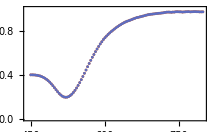

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,2750,25];
lambda = wl[[take]];
pol = 2;

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

### BestRadiusCfrac - 0

```mathematica
fileName = FileNames["0*BestRadiusCFracFit-PPol*.csv",{"0*Fit-p*"}]
data = Drop[Import[#,"Data"],1]&/@ fileName
```

{0-Fit-p-Pol/0-BestRadiusCFracFit-PPol-450nm-750nm.csv,0-Fit-p-Pol/0-BestRadiusCFracFit-PPol-450nm-800nm.csv,0-Fit-p-Pol/0-BestRadiusCFracFit-PPol-450nm-850nm.csv}

{{{p Pol,64.9,5.78,13.4038,0.292934,1.81801},{p Pol,64.9,7.3,4.07046,0.148597,5.98483×10^-7},{p Pol,72.9,5.78,3.36064,-0.187307,4.87805×10^-7},{p Pol,72.9,7.3,4.14053,0.207798,5.9454×10^-7}},{{p Pol,64.9,5.78,3.34602,0.138901,4.98174×10^-7},{p Pol,64.9,7.3,4.07073,0.146939,5.60578×10^-7},{p Pol,72.9,5.78,2.60397,3.86635,1.21705×10^-10},{p Pol,72.9,7.3,4.15422,0.207049,5.51664×10^-7}},{{p Pol,64.9,5.78,3.36366,0.13879,8.85535×10^-7},{p Pol,64.9,7.3,4.09755,0.145596,1.00663×10^-6},{p Pol,72.9,5.78,1.69209,-3.83682,1.04237×10^-10},{p Pol,72.9,7.3,4.17573,0.206782,9.86411×10^-7}}}

#### 450nm-750nm

```mathematica
i = 1;
```

```mathematica
radpPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{13.4038,4.07046},{3.36064,4.14053}}

{{0.292934,0.148597},{0.187307,0.207798}}

{{1,1},{1,1}}

{{1.81801,5.98483×10^-7},{4.87805×10^-7,5.9454×10^-7}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

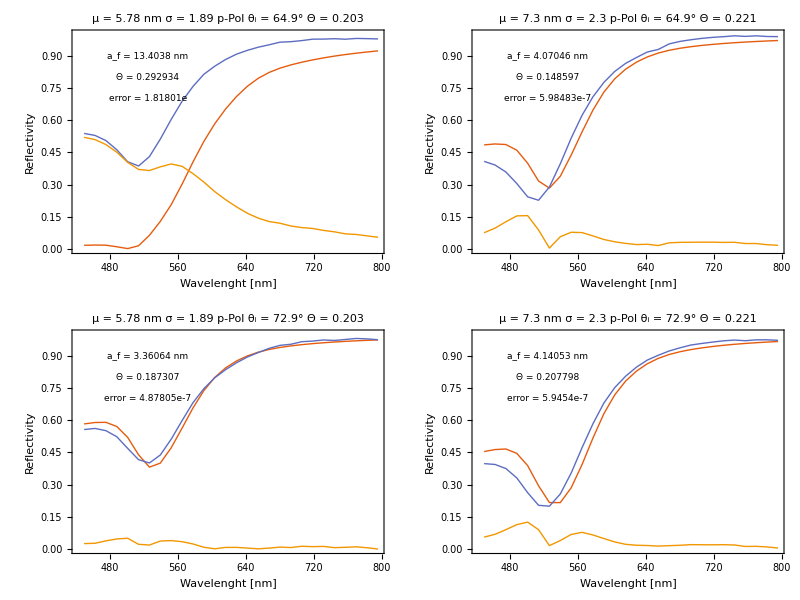

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{525,.90}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{525,.80}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{525,.70}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-p-Pol/0-BestRadiusCFracFit-PPol-450nm-750nm.pdf

#### 450nm-800nm

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.34602,4.07073},{2.60397,4.15422}}

{{0.138901,0.146939},{3.86635,0.207049}}

{{1,1},{1,1}}

{{4.98174×10^-7,5.60578×10^-7},{1.21705×10^-10,5.51664×10^-7}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

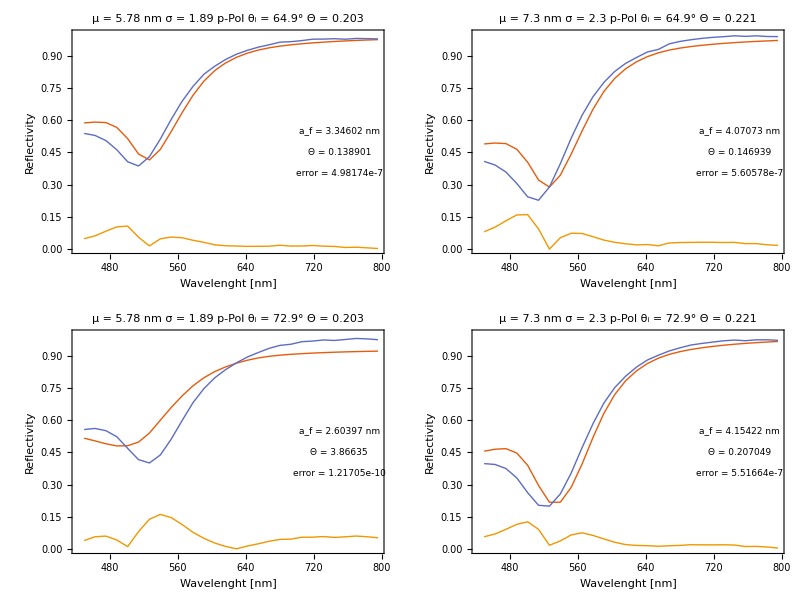

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{750,.55}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{750,.45}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{750,.35}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-p-Pol/0-BestRadiusCFracFit-PPol-450nm-800nm.pdf

#### 450nm-850nm

```mathematica
i = 3;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.36366,4.09755},{1.69209,4.17573}}

{{0.13879,0.145596},{3.83682,0.206782}}

{{1,1},{1,1}}

{{8.85535×10^-7,1.00663×10^-6},{1.04237×10^-10,9.86411×10^-7}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

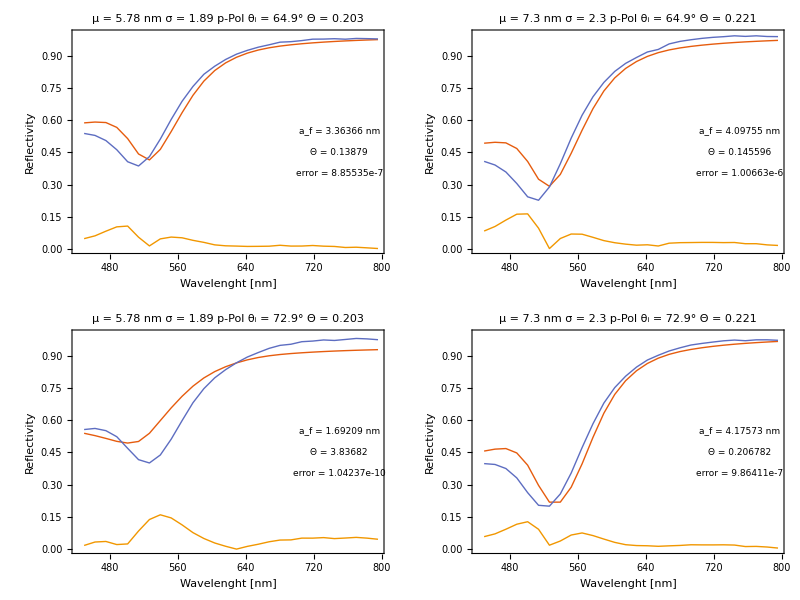

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{750,.55}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{750,.45}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{750,.35}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-s-Pol/0-BestRadiusCFracFit-SPol-450nm-850nm.pdf

### BestRadiusCfrac - 1 ***

```mathematica
pol = 2;
fileName = FileNames["1*BestRadiusCFracFit-PPol*.csv",{"0*Fit-p*"}]
data = Drop[Import[#,"Data"],1]&/@ fileName
cfracLabels = {};
```

{0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm.csv,0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-850nm.csv}

{{{p Pol,64.9,5.78,3.29306,-0.141118,1.19568×10^-6},{p Pol,64.9,7.3,4.02642,0.152183,1.29604×10^-6},{p Pol,72.9,5.78,3.33799,-0.188647,1.0952×10^-6},{p Pol,72.9,7.3,4.10893,0.209861,1.31247×10^-6}},{{p Pol,64.9,5.78,3.36127,0.139131,4.50373×10^-7},{p Pol,64.9,7.3,4.09503,0.14605,5.11504×10^-7},{p Pol,72.9,5.78,1.69531,-3.86451,5.11073×10^-11},{p Pol,72.9,7.3,4.17023,0.207202,4.99753×10^-7}}}

#### 450nm-700nm ***

```mathematica
i = 1;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2];
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}];
errorsPol = Partition[#[[6]]&/@ data[[i]],2];

indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

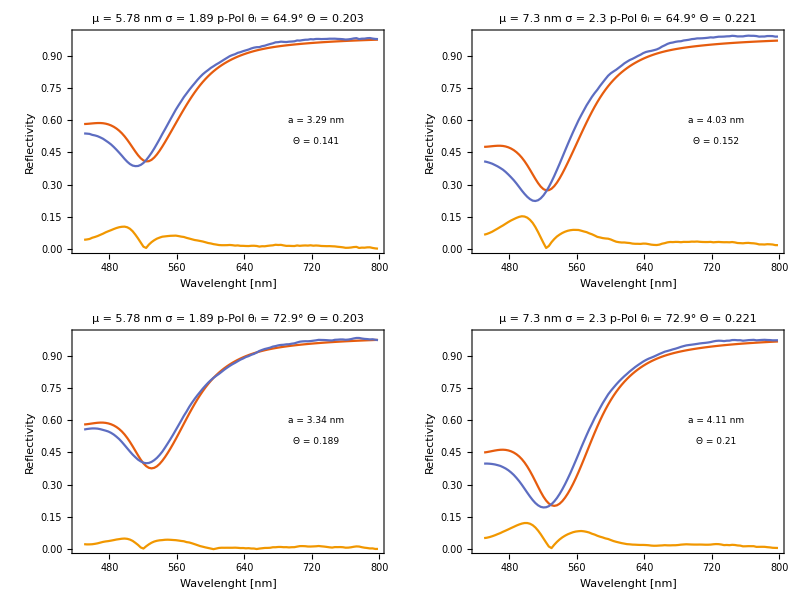

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

#### 450nm-700nm (Selected Θ)

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2];
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
cfracsPol[[1]] = cfracsPol[[2]] 
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}];
errorsPol = Partition[#[[6]]&/@ data[[i]],2];

indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo4 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

{{0.141118,0.152183},{0.188647,0.209861}}

{0.188647,0.209861}

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

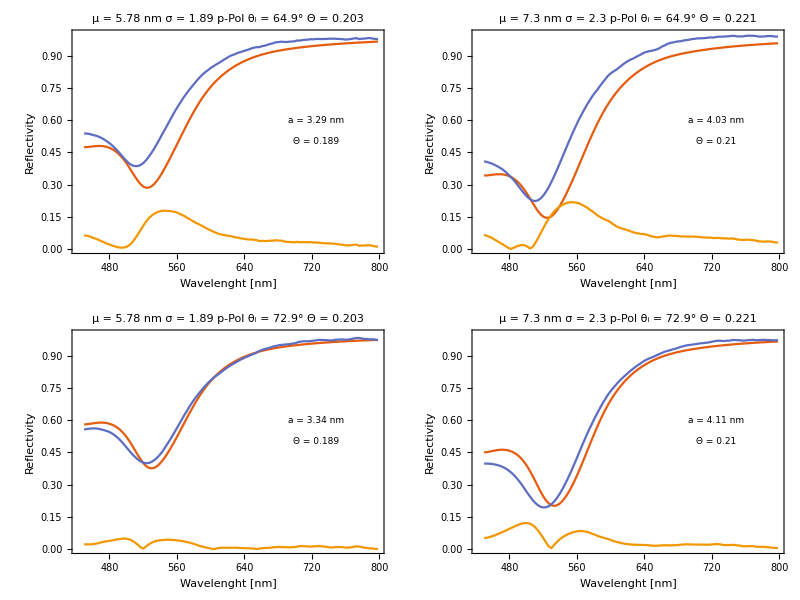

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm_MOD.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo4,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"_MOD.pdf"],plot]
```

#### 450nm-700nm (Selected Θ)

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2];
cfracsPol = {{.17,.19},{.17,.19}};
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}];
errorsPol = Partition[#[[6]]&/@ data[[i]],2];

indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo5 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

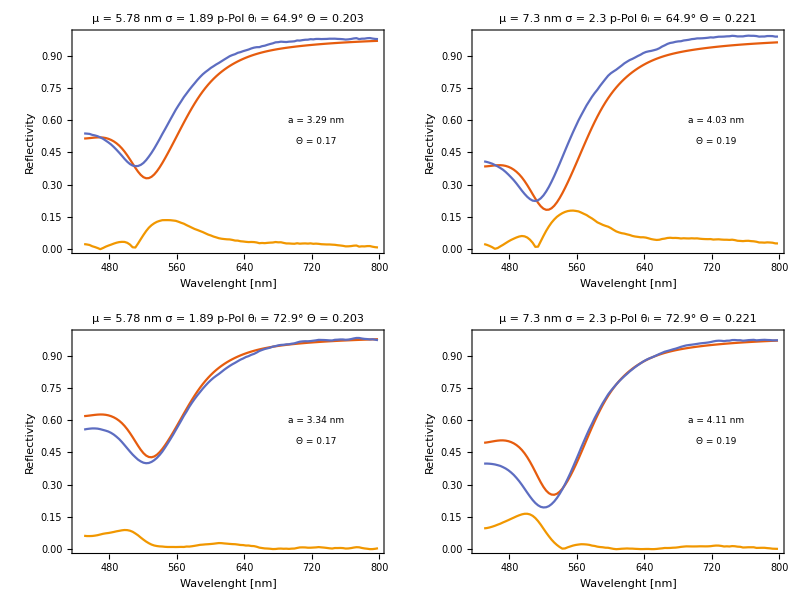

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm_MOD.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo5,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"_MOD.pdf"],plot]
```

#### 450nm-700nm (Selected Θ)

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2];
cfracsPol = {{.17,.19},{.17,.19}}+.02;
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}];
errorsPol = Partition[#[[6]]&/@ data[[i]],2];

indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo6 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

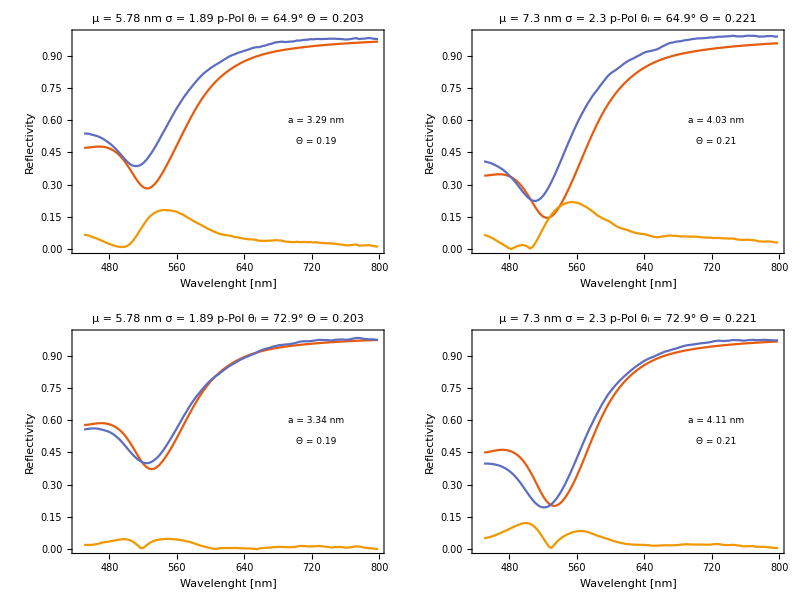

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm_MOD2.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo6,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"_MOD2.pdf"],plot]
```

#### 450nm-700nm (Selected Θ)

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2];
cfracsPol = {{.17,.19},{.17,.19}}+.03;
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}];
errorsPol = Partition[#[[6]]&/@ data[[i]],2];

indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo7 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

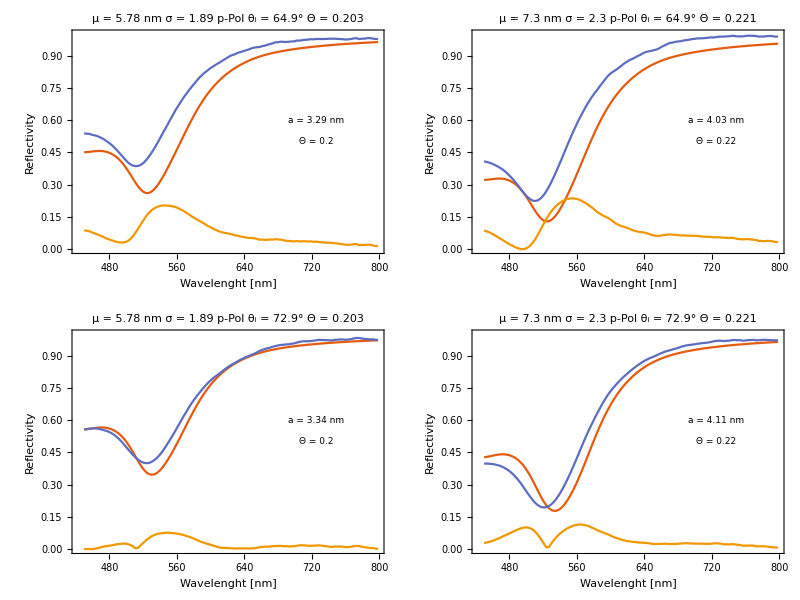

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm_MOD3.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo7,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"_MOD3.pdf"],plot]
```

#### 450nm-850nm

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.36127,4.09503},{1.69531,4.17023}}

{{0.139131,0.14605},{3.86451,0.207202}}

{{1,1},{1,1}}

{{4.50373×10^-7,5.11504×10^-7},{5.11073×10^-11,4.99753×10^-7}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Function::slotn: Slot number 1 in (a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])& cannot be filled from ((a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])&)[].

Function::slotn: Slot number 2 in (a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])& cannot be filled from ((a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])&)[].

Function::slotn: Slot number 1 in (a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])& cannot be filled from ((a=radsPol⟦#1,#2⟧;cf=cfracsPol⟦#1,#2⟧;b=offsPol⟦#1,#2⟧;sigma=muSigma⟦#2,2⟧;f=b norm2[CSMBioReflectionInt[Part[«2»],indAu,lambda,cf,{«2»},Rule[«2»]]⟦pol⟧])&)[].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

Part::pkspec1: The expression #1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

CSM::cfrac: The coverage fraction {{0.139131,0.14605},{3.86451,0.207202}}⟦#1,#2⟧ must be a scalar.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{750,.55}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{750,.45}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{750,.35}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

MapThread::mptd: Object Conjugate[Null⟦2⟧] Null⟦2⟧ {{1,1},{1,1}}⟦#1,#2⟧ at position {2, 1} in … has only 0 of required 2 dimensions.

Grid[MapThread[ListLinePlot[{#1,#2⟦take,2⟧,Abs[#1-#2⟦take,2⟧]},DataRange→lambda⟦{1,-1}⟧,PlotRange→1,PlotLabel→Style[#3,texStyle],Evaluate[graphsOptsExp],FrameLabel→{Style[Wavelenght [nm],texStyle],Style[Reflectivity,texStyle]},Epilog→{Inset[Style[a_f = <>ToString[#4]<> nm,texStyle],{750,0.55}],Inset[Style[Θ = <>ToString[#5],texStyle],{750,0.45}],Inset[Style[error = <>ToString[Slot[7e]],texStyle],{750,0.35}]}]&,{Conjugate[Null⟦2⟧] Null⟦2⟧ {{1,1},{1,1}}⟦#1,#2⟧,5,{{4.50373×10^-7,5.11504×10^-7},{5.11073×10^-11,4.99753×10^-7}}},2]]
 |  |  |  |

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-850nm.pdf

### Final

```mathematica
NumberForm[.141118,2]
```

0.14

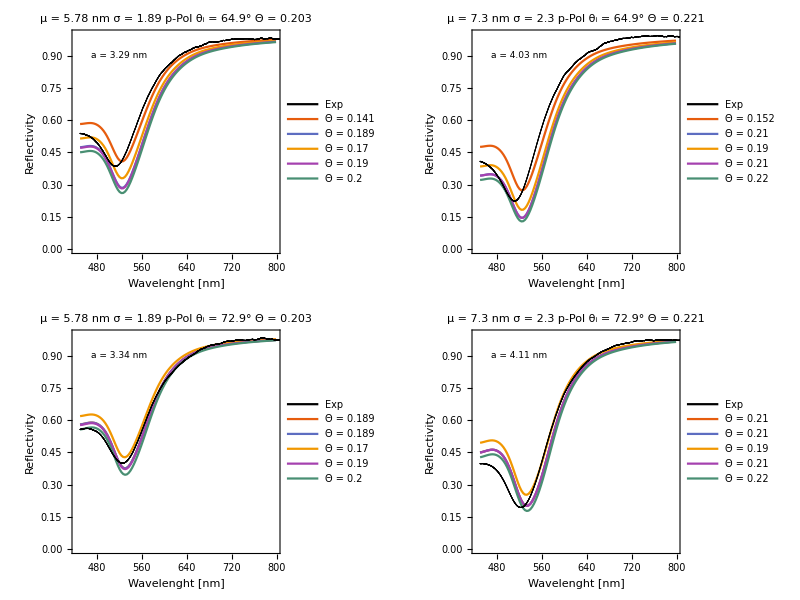

0-Fit-p-Pol/1-BestRadiusCFracFit-PPol-450nm-700nm_All.pdf

```mathematica
pos = {520, .9};
plot = Grid[MapThread[
  Show[{
ListLinePlot[{#1,#3,#4,#8,#9},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#5,texStyle],Evaluate[graphsOptsExp],FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
PlotLegends->Placed[LineLegend[Prepend[colors[[;;8]],Black],(Style[#,texStyle]&/@{"Exp","Θ = "<>ToString[NumberForm[#7[[1]],3]],"Θ = "<>ToString[NumberForm[#7[[2]],3]],"Θ = "<>ToString[NumberForm[#7[[3]],3]],"Θ = "<>ToString[NumberForm[#7[[4]],3]],"Θ = "<>ToString[NumberForm[#7[[5]],3]]}),Spacings->.1],{Right,Center}],
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#6,3]<>" nm",texStyle],pos]}]
,
ListPlot[#2,PlotStyle->Directive[Black],Mesh->All]}]&,{algo3,spectra[[pol]],algo4,algo5,lb,radsPol,Transpose[cfracLabels,{3,1,2}],algo6,algo7},2]]
Export[StringReplace[fileName[[i]],".csv"->"_All.pdf"],plot]
```

## FitModel (Gradient Descend) s Pol

{2,2,2,3138,2}

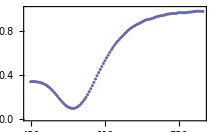
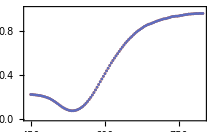
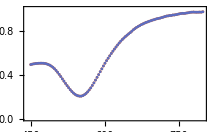
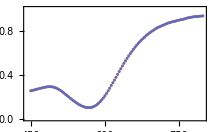

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,2750,25];
lambda = wl[[take]];
pol = 1;

Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

### BestRadiusCfrac - 0

```mathematica
fileName = FileNames["0*BestRadiusCFracFit-SPol*.csv",{"0*Fit-s*"}]
data = Drop[Import[#,"Data"],1]&/@ fileName
```

{0-Fit-s-Pol/0-BestRadiusCFracFit-SPol-450nm-800nm.csv,0-Fit-s-Pol/0-BestRadiusCFracFit-SPol-450nm-850nm.csv}

{{{s Pol,64.9,5.78,3.52662,0.406405,7.79679×10^-8},{s Pol,64.9,7.3,6.77372,0.577651,8.47363×10^-12},{s Pol,72.9,5.78,3.43854,-0.359409,2.11982×10^-7},{s Pol,72.9,7.3,4.52619,0.489063,8.15068×10^-8}},{{s Pol,64.9,5.78,3.57025,0.399926,1.49219×10^-7},{s Pol,64.9,7.3,5.79628,0.505644,1.50015×10^-8},{s Pol,72.9,5.78,1.39737,-1.73394,2.90424×10^-8},{s Pol,72.9,7.3,4.55205,0.487685,1.56815×10^-7}}}

#### 450nm-800nm

```mathematica
i = 1;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.52662,6.77372},{3.43854,4.52619}}

{{0.406405,0.577651},{0.359409,0.489063}}

{{1,1},{1,1}}

{{7.79679×10^-8,8.47363×10^-12},{2.11982×10^-7,8.15068×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

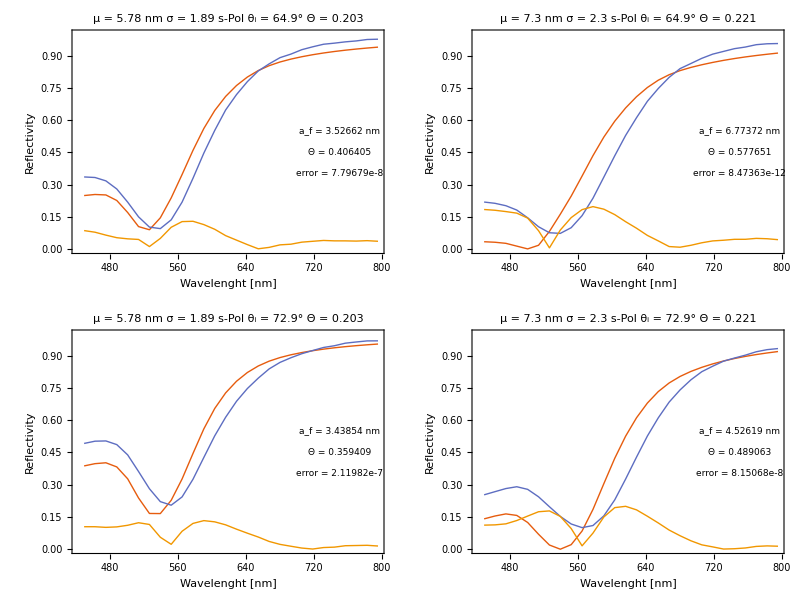

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{750,.55}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{750,.45}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{750,.35}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-s-Pol/0-BestRadiusCFracFit-SPol-450nm-800nm.pdf

#### 450nm-850nm

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.57025,5.79628},{1.39737,4.55205}}

{{0.399926,0.505644},{1.73394,0.487685}}

{{1,1},{1,1}}

{{1.49219×10^-7,1.50015×10^-8},{2.90424×10^-8,1.56815×10^-7}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radpPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

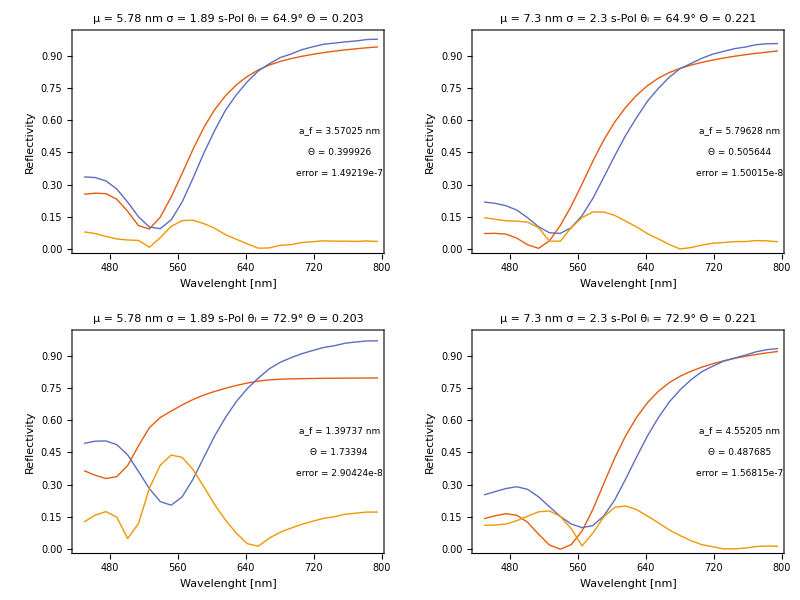

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a_f = "<> ToString@#4<>" nm",texStyle],{750,.55}],
Inset[Style["Θ = "<> ToString@#5,texStyle],{750,.45}],
Inset[Style["error = "<>ToString[ScientificForm[#7, NumberFormat -> (Row[{#1, "e", #3}] &)]],texStyle],{750,.35}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

```mathematica
Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

0-Fit-s-Pol/0-BestRadiusCFracFit-SPol-450nm-850nm.pdf

### BestRadiusCfrac - 1***

```mathematica
pol = 1;
fileName = FileNames["1*BestRadiusCFracFit-SPol*.csv",{"0*Fit-s*"}]
data = Drop[Import[#,"Data"],1]&/@ fileName
cfracLabels = {};
```

{0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-650nm.csv,0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nm.csv}

{{{s Pol,64.9,5.78,3.41467,0.440446,1.29383×10^-7},{s Pol,64.9,7.3,2.74106,0.647949,2.59636×10^-9},{s Pol,72.9,5.78,3.34352,0.360287,5.19649×10^-7},{s Pol,72.9,7.3,4.31888,0.47367,1.62998×10^-7}},{{s Pol,64.9,5.78,3.56408,0.398191,7.71757×10^-8},{s Pol,64.9,7.3,5.29364,0.498063,1.1743×10^-8},{s Pol,72.9,5.78,3.45347,-0.356801,1.95464×10^-7},{s Pol,72.9,7.3,4.53863,0.48575,8.12872×10^-8}}}

#### 450nm-850nm***

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2]
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{0.398191,0.498063},{0.356801,0.48575}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo3 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

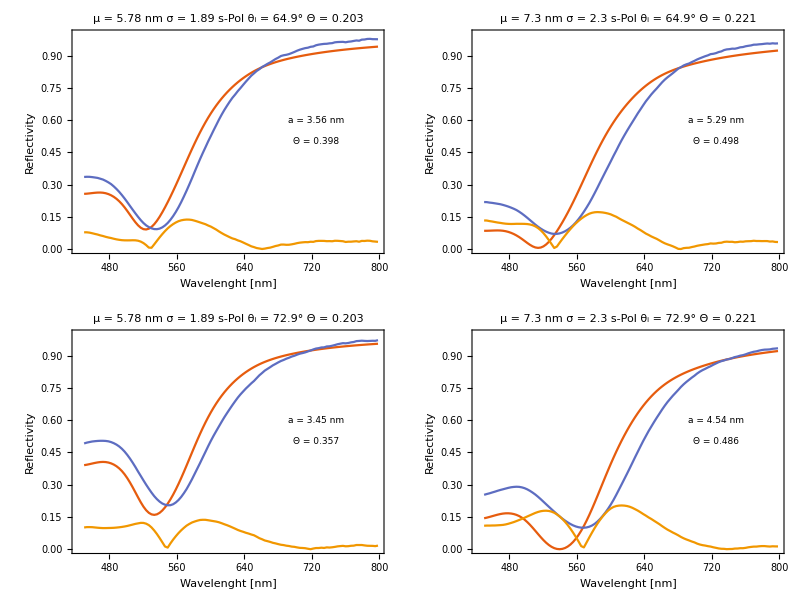

0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nm.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo3,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->".pdf"],plot]
```

#### 450nm-850nm (Selected Θ p Pol)

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
cfracsPol = {{0.14111843243893823,0.15218334022103389},{0.18864684503923082,0.20986111583047243}};
AppendTo[cfracLabels,cfracsPol];
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo4 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

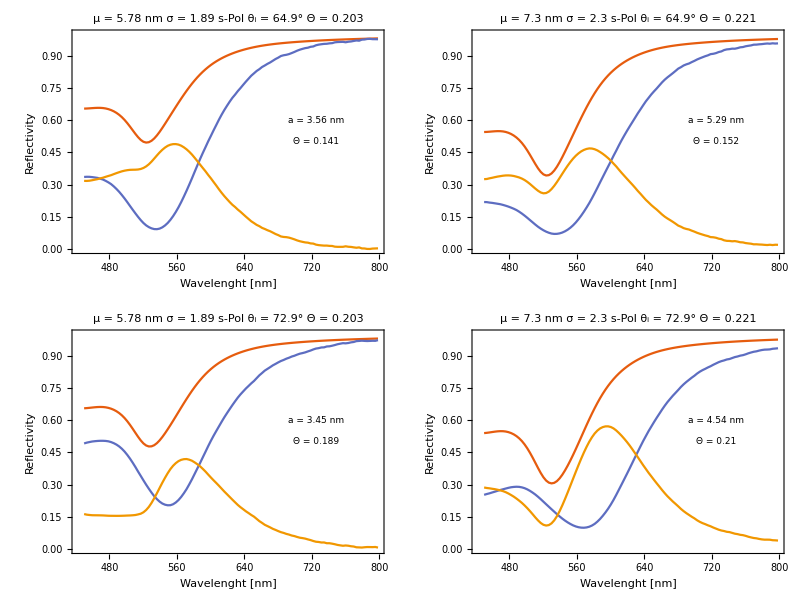

0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nmMODpCfrac.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo4,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"MODpCfrac.pdf"],plot]
```

#### 450nm-850nm (Selected Θ p Pol)

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
cfracsPol = {{0.18864684503923082,0.20986111583047243},{0.18864684503923082,0.20986111583047243}};
AppendTo[cfracLabels,cfracsPol]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{{0.398191,0.498063},{0.356801,0.48575}},{{0.141118,0.152183},{0.188647,0.209861}},{{0.188647,0.209861},{0.188647,0.209861}}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo5 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

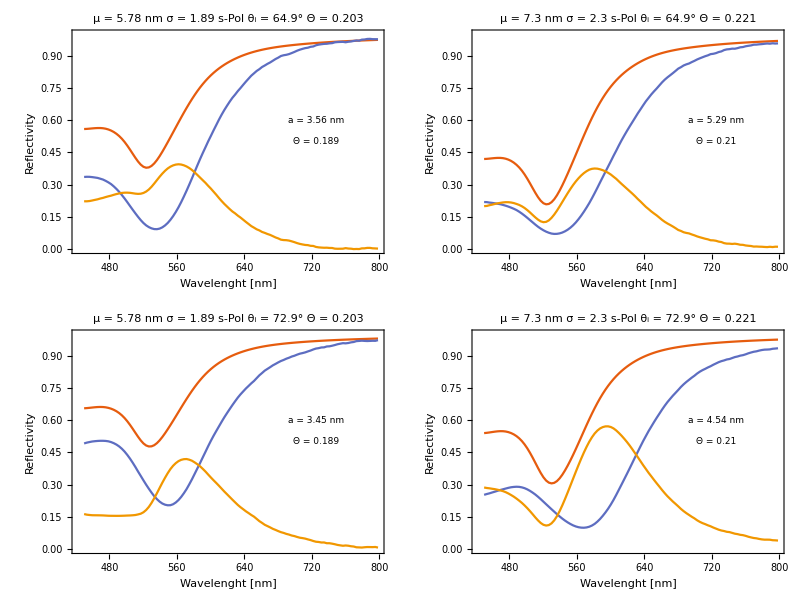

0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nmMODpCfrac-1.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo5,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"MODpCfrac-1.pdf"],plot]
```

#### 450nm-850nm (Selected Θ p Pol)

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
cfracsPol = {{0.20,0.22},{0.20,0.22}};
AppendTo[cfracLabels,cfracsPol]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{{0.398191,0.498063},{0.356801,0.48575}},{{0.141118,0.152183},{0.188647,0.209861}},{{0.188647,0.209861},{0.188647,0.209861}},{{0.2,0.22},{0.2,0.22}}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo7 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

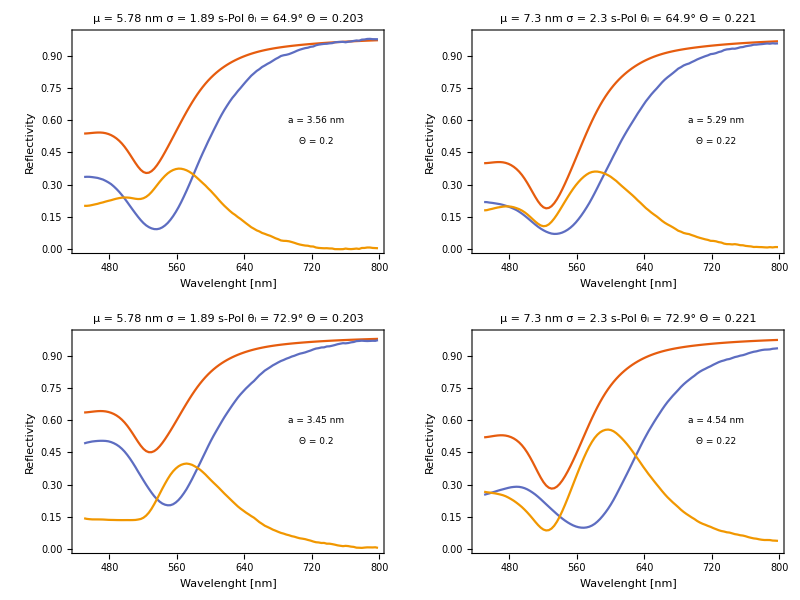

```mathematica
plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo7,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

#### 450nm-850nm (Selected Θ p Pol)

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
cfracsPol = .05+{{0.20,0.22},{0.20,0.22}};
AppendTo[cfracLabels,cfracsPol]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{{0.398191,0.498063},{0.356801,0.48575}},{{0.141118,0.152183},{0.188647,0.209861}},{{0.188647,0.209861},{0.188647,0.209861}},{{0.2,0.22},{0.2,0.22}},{{0.25,0.27},{0.25,0.27}}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo8 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

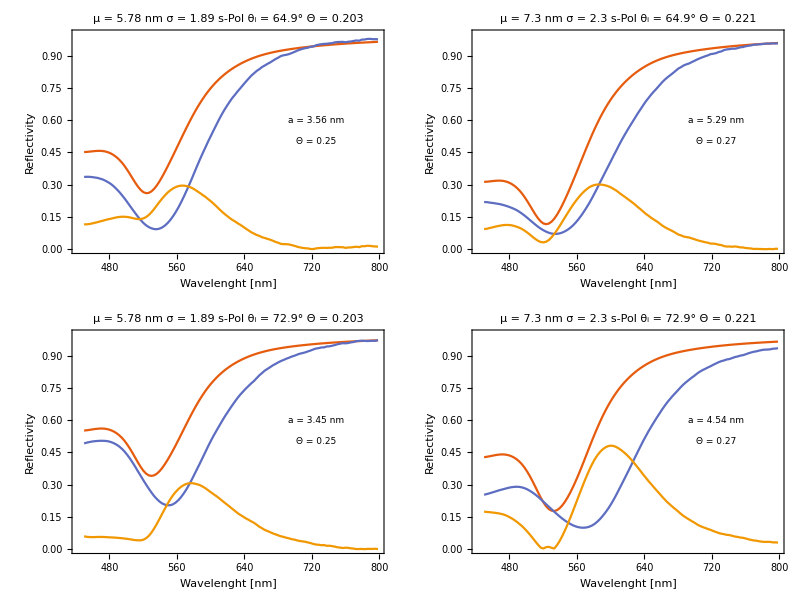

0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nmMODpCfrac-1.pdf

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#4,3]<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@NumberForm[#5,3],texStyle],pos+{0,-.1}]
}]&,{algo8,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]

Export[StringReplace[fileName[[i]],".csv"->"MODpCfrac-1.pdf"],plot]
```

#### 450nm-850nm (Selected Θ p Pol)

```mathematica
i = 2;
```

```mathematica
radsPol = Partition[#[[4]]&/@ data[[i]],2]
cfracsPol = Partition[Abs[#[[5]]]&/@ data[[i]],2];
cfracsPol = .1+{{0.20,0.22},{0.20,0.22}};
AppendTo[cfracLabels,cfracsPol]
offsPol = ConstantArray[1,{2,2}]
errorsPol = Partition[#[[6]]&/@ data[[i]],2]
```

{{3.56408,5.29364},{3.45347,4.53863}}

{{{0.398191,0.498063},{0.356801,0.48575}},{{0.141118,0.152183},{0.188647,0.209861}},{{0.188647,0.209861},{0.188647,0.209861}},{{0.2,0.22},{0.2,0.22}},{{0.25,0.27},{0.25,0.27}},{{0.3,0.32},{0.3,0.32}}}

{{1,1},{1,1}}

{{7.71757×10^-8,1.1743×10^-8},{1.95464×10^-7,8.12872×10^-8}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
algo9 = Array[(a = radsPol[[#1,#2]];
            cf = cfracsPol[[#1,#2]];
            b = offsPol[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = b*norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
Dimensions[radsPol]];(*pol, ang,case*)

lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polL = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@{cfrac,cfrac}[[#1,#2]];
       deg = "θ_i = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polL<>" "<>deg<>" "<>cf)&,
{2,2}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

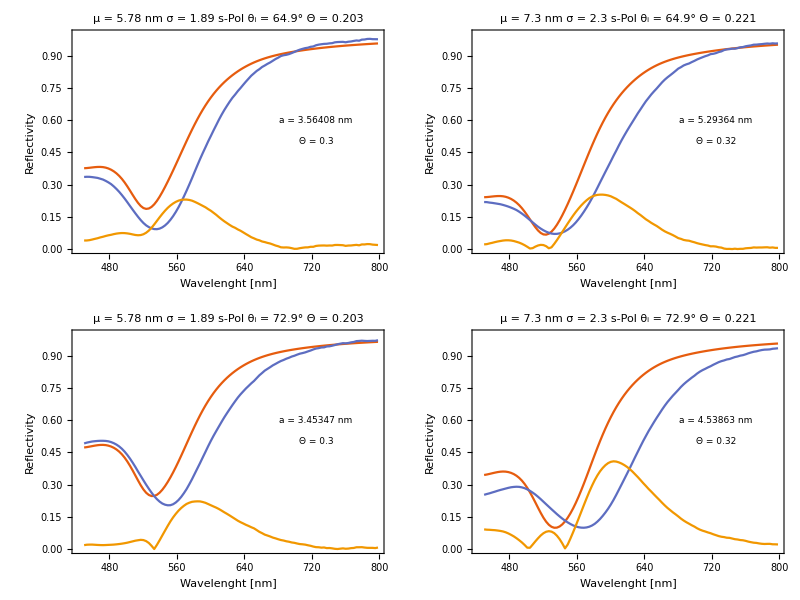

```mathematica
pos = {725, .6};

plot = Grid@MapThread[ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsExp],
FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
Epilog->{Inset[Style["a = "<> ToString@#4<>" nm",texStyle],pos],
Inset[Style["Θ = "<> ToString@#5,texStyle],pos+{0,-.1}]
}]&,{algo9,spectra[[pol]],lb,radsPol,cfracsPol,offsPol,errorsPol},2]
```

### Final

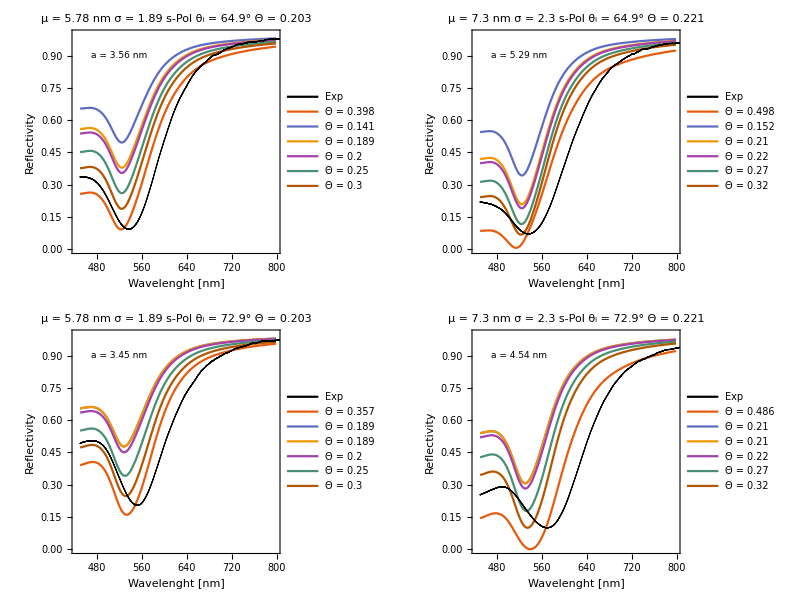

0-Fit-s-Pol/1-BestRadiusCFracFit-SPol-450nm-850nm_All.pdf

```mathematica
pos = {520, .9};
plot = Grid[MapThread[
  Show[{
ListLinePlot[{#1,#3,#4,#5,#6,#7},DataRange->lambda[[{1,-1}]],PlotRange->1,PlotLabel->Style[#8,texStyle],Evaluate[graphsOptsExp],FrameLabel->{Style["Wavelenght [nm]",texStyle],Style["Reflectivity",texStyle]},
PlotLegends->Placed[LineLegend[Prepend[colors[[;;7]],Black],(Style[#,texStyle]&/@Flatten[{"Exp",Table["Θ = "<>ToString[NumberForm[#10[[i]],3]],{i,Length[#10]}]}]),Spacings->.1],{Right,Center}],
Epilog->{Inset[Style["a = "<> ToString@NumberForm[#9,3]<>" nm",texStyle],pos]}]
,
ListPlot[#2,PlotStyle->Directive[Black],Mesh->All]}]&,{algo3,spectra[[pol]],algo4,algo5,algo7,algo8,algo9,lb,radsPol,Transpose[cfracLabels,{3,1,2}]},2]]
Export[StringReplace[fileName[[i]],".csv"->"_All.pdf"],plot]
```